```mathematica
Clear[x,θ,t,Vy,Vx,g,V]
Solve[Vy*t-1/2*g*t^2==0,t][[2]];
x=Vx*t/.%;
x=x/.Vx->Cos[θ]*V/.Vy->Sin[θ]*V;
Solve[D[x,θ]==0,θ][[3]]
TextCell["this shows that the displacement x, is maximized when θ= π/4 or 45 Degrees."]
Solve[2*V^2/9.8==100,V][[2]];
TextCell["this shows that the velocity components (Vx=Vy) neccessary to reach PCC is 22.1259 m/s"]
```

{θ→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers]}

this shows that the displacement x, is maximized when θ= π/4 or 45 Degrees.

{{V→-22.1359},{V→22.1359}}

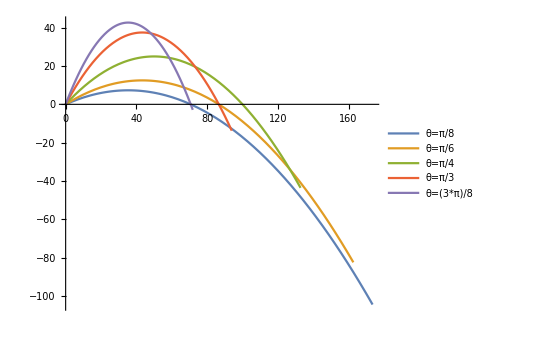

```mathematica
Clear[x,θ,t,Vy,Vx,g,V]
V=Sqrt[2]*22.1359;
g=9.8;
eqs = {x''[t]==0,y''[t]==-g};
θ1=π/8;
ini1= {x[0]==0,y[0]==0, x'[0]==Cos[θ1]*V, y'[0]==Sin[θ1]*V};
rules1=NDSolve[Join[eqs,ini1],{x,y},{t,0,5}];
xx1[t_]:=x[t]/.rules1[[1]];
yy1[t_]:=y[t]/.rules1[[1]];
θ2=π/6;
ini2= {x[0]==0,y[0]==0, x'[0]==Cos[θ2]*V, y'[0]==Sin[θ2]*V};
rules2=NDSolve[Join[eqs,ini2],{x,y},{t,0,5}];
xx2[t_]:=x[t]/.rules2[[1]];
yy2[t_]:=y[t]/.rules2[[1]];
θ3=π/4;
ini3= {x[0]==0,y[0]==0, x'[0]==Cos[θ3]*V, y'[0]==Sin[θ3]*V};
rules3=NDSolve[Join[eqs,ini3],{x,y},{t,0,5}];
xx3[t_]:=x[t]/.rules3[[1]];
yy3[t_]:=y[t]/.rules3[[1]];
θ4=π/3;
ini4= {x[0]==0,y[0]==0, x'[0]==Cos[θ4]*V, y'[0]==Sin[θ4]*V};
rules4=NDSolve[Join[eqs,ini4],{x,y},{t,0,5}];
xx4[t_]:=x[t]/.rules4[[1]];
yy4[t_]:=y[t]/.rules4[[1]];
θ5=(3*π)/8;
ini5= {x[0]==0,y[0]==0, x'[0]==Cos[θ5]*V, y'[0]==Sin[θ5]*V};
rules5=NDSolve[Join[eqs,ini5],{x,y},{t,0,5}];
xx5[t_]:=x[t]/.rules5[[1]];
yy5[t_]:=y[t]/.rules5[[1]];
ParametricPlot[{{xx1[t],yy1[t]},{xx2[t],yy2[t]},{xx3[t],yy3[t]},{xx4[t],yy4[t]},{xx5[t],yy5[t]}},{t,0,6},PlotLegends->{"θ=π/8","θ=π/6","θ=π/4","θ=π/3","θ=(3*π)/8"}]
```

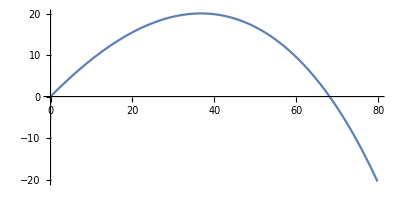

```mathematica
Clear[x,θ,t,Vy,Vx,g,V]
m = 0.5;
r= 0.05;
g = 9.8;
p= 1.3;
V=Sqrt[2]*22.1359;
eqs = {x''[t]==-Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*x'[t], y''[t]== -g -Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*y'[t]};
θ= π/4;
ini = {x[0]==0, y[0]== 0, x'[0]==Cos[θ]*V, y'[0]==Sin[θ]*V};
rules= NDSolve[Join[eqs,ini],{x,y},{t,0,3}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];

ParametricPlot[{xx[t],yy[t]},{t,0,5}]
TextCell["the grapefruit will land around 67 meters away"]
```

42.9

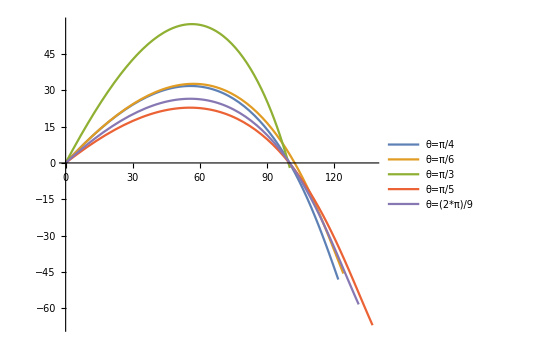

The Optimal firing angle is between 2π/9 and π/4

```mathematica
(*4*)
Clear[x,θ,t,Vy,Vx,g,V]
m = 0.5;
r= 0.05;
g = 9.8;
p= 1.3;
V1=Sqrt[2]*22.1359;
eqs = {x''[t]==-Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*x'[t], y''[t]== -g -Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*y'[t]};
V1=42.1;
θ1= π/4;
ini1 = {x[0]==0, y[0]== 0, x'[0]==Cos[θ1]*V1, y'[0]==Sin[θ1]*V1};
rules1= NDSolve[Join[eqs,ini1],{x,y},{t,0,3}];
xx1[t_]:=x[t]/.rules1[[1]];
yy1[t_]:=y[t]/.rules1[[1]];
V2=42.9
θ2= π/6;
ini2 = {x[0]==0, y[0]== 0, x'[0]==Cos[θ1]*V2, y'[0]==Sin[θ1]*V2};
rules2= NDSolve[Join[eqs,ini2],{x,y},{t,0,3}];
xx2[t_]:=x[t]/.rules2[[1]];
yy2[t_]:=y[t]/.rules2[[1]];
V3=49.6;
θ3= π/3;
ini3 = {x[0]==0, y[0]== 0, x'[0]==Cos[θ3]*V3, y'[0]==Sin[θ3]*V3};
rules3= NDSolve[Join[eqs,ini3],{x,y},{t,0,3}];
xx3[t_]:=x[t]/.rules3[[1]];
yy3[t_]:=y[t]/.rules3[[1]];
V4=42.1;
θ4= π/5;
ini4 = {x[0]==0, y[0]== 0, x'[0]==Cos[θ4]*V4, y'[0]==Sin[θ4]*V4};
rules4= NDSolve[Join[eqs,ini4],{x,y},{t,0,3}];
xx4[t_]:=x[t]/.rules4[[1]];
yy4[t_]:=y[t]/.rules4[[1]];
V5=41.8;
θ5= (2π)/9;
ini5 = {x[0]==0, y[0]== 0, x'[0]==Cos[θ5]*V5, y'[0]==Sin[θ5]*V5};
rules5= NDSolve[Join[eqs,ini5],{x,y},{t,0,3}];
xx5[t_]:=x[t]/.rules5[[1]];
yy5[t_]:=y[t]/.rules5[[1]];
ParametricPlot[{{xx1[t],yy1[t]},{xx2[t],yy2[t]},{xx3[t],yy3[t]},{xx4[t],yy4[t]},{xx5[t],yy5[t]}},{t,0,7},PlotLegends->{"θ=π/4","θ=π/6","θ=π/3","θ=π/5","θ=(2*π)/9"}]
TextCell["The Optimal firing angle is between 2π/9 and π/4 "]
```

```mathematica
(*5a)*)
Clear[x,θ,t,Vy,Vx,g,V]
m = 0.5;
r= 0.05;
g = 9.8;
p= 1.3;
V1=Sqrt[2]*22.1359;
θ1= π/4;
(*eqs = {x''[t]==(-1*p*r^2*Sqrt[x'[t]^2*y'[t]^2])/m*x'[t], y''[t]== -g +(-1*p*r^2*Sqrt[x'[t]^2*y'[t]^2])/m*y'[t]};
ini = {x[0]==0, y[0]== 0, x'[0]==Cos[θ]*V, y'[0]==Sin[θ]*V};*)

landtime[V_,θ_]:=t /.FindRoot[0==y[t]/.NDSolve[{x''[t]==-Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*x'[t], y''[t]== -g -Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*y'[t],x[0]==0, y[0]== 0, x'[0]==Cos[θ]*V, y'[0]==Sin[θ]*V},{x,y},{t,0,100}][[1]],{t,10}][[1]]
landtime[V1,θ1]
(*part b)*)
range[V_,θ_]:=x[landtime[V,θ]]/.NDSolve[{x''[t]==-Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*x'[t], y''[t]== -g -Abs[-1*p*r^2*Sqrt[x'[t]^2+y'[t]^2]]/m*y'[t],x[0]==0, y[0]== 0, x'[0]==Cos[θ]*V, y'[0]==Sin[θ]*V},{x,y},{t,0,100}][[1]]
range[V1,θ1]
(*part c)*)
targetvelocity[θ_,d_]:=Module[{Vr=100,Vl=0},While[Abs[range[Vr,θ]-d]>10^-6,If[range[Vr,θ]>d,V1=Vr;Vr=Vr-Abs[Vr-Vl]/2;;Vl=V1,V1=Vr;Vr=Vr+Abs[Vr-Vl]/2;Vl=V1]];N[Vr]]
targetvelocity[θ1,100]
bestangle[d_]:=Module[{ θr=π/4,θl=π/5},While[targetvelocity[θr,d]>targetvelocity[θr-10^-3,d]||targetvelocity[θr,d]>targetvelocity[θr+10^-3,d],If[targetvelocity[θr,d]>targetvelocity[θr-Abs[θr-θl]/2,d],θ1=θr;θr=θr-Abs[θr-θl]/2;θl=θ1,θ1=θr;θr=θr+Abs[θr-θl]/2;θl=θ1]Print[θr]];θr]
bestangle[100]
```

4.03457

68.1017

42.1045

(9 π)/40

(19 π)/80

(37 π)/160

(73 π)/320

(29 π)/128

(289 π)/1280

(577 π)/2560

(577 π)/2560